Simulating nonnative cubic interactions on noisy quantum machines

arXiv:2004.06885

Notebook: Óscar Amaro, February 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce figure 2 from the paper.

h=(0 | √2 ⅇ^(ⅈ θ) √(-1+s) | 0
√2 ⅇ^(-ⅈ θ) √(-1+s) | 0 | √2 ⅇ^(ⅈ θ) √s
0 | √2 ⅇ^(-ⅈ θ) √s | 0)

e^-I h τ =((s+(-1+s) Cos[√(-2+4 s) τ])/(-1+2 s) | (√(-1+s) (-ⅈ Cos[θ]+Sin[θ]) Sin[√(-2+4 s) τ])/(√(-1+2 s)) | -(2 ⅇ^(2 ⅈ θ) √(-1+s) √s Sin[√(-1/2+s) τ]^2)/(-1+2 s)
(√(-1+s) (-ⅈ Cos[θ]-Sin[θ]) Sin[√(-2+4 s) τ])/(√(-1+2 s)) | Cos[√(-2+4 s) τ] | (√s (-ⅈ Cos[θ]+Sin[θ]) Sin[√(-2+4 s) τ])/(√(-1+2 s))
-(2 ⅇ^(-2 ⅈ θ) √(-1+s) √s Sin[√(-1/2+s) τ]^2)/(-1+2 s) | (√s (-ⅈ Cos[θ]-Sin[θ]) Sin[√(-2+4 s) τ])/(√(-1+2 s)) | (-1+s+s Cos[√(-2+4 s) τ])/(-1+2 s))

U=(0.960794 | 0.271664 | 0.0554462 | 0
-0.271664 | 0.882381 | 0.384191 | 0
0.0554462 | -0.384191 | 0.921587 | 0
0 | 0 | 0 | 1)

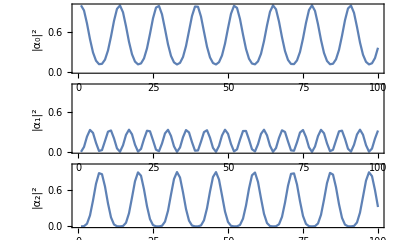

```mathematica
(* clear variables *)
Clear[h,s,λ,θ,τ,U,psi,psi0]

(* Hamiltonian from equation 11 *)
h={{0,Exp[I θ]Sqrt[2 (s-1)],0},{Exp[-I θ]Sqrt[2 (s-1)],0,Exp[I θ]Sqrt[2 s]},{0,Exp[-I θ]Sqrt[2 s],0}};
Print["h=",h//MatrixForm]

(* exponentiate Hamiltonian *)
exph=MatrixExp[- I h τ]//FullSimplify;
Print["e^-I h τ =",exph//MatrixForm]

(* embed U in 4x4 matrix *)
U=IdentityMatrix[4];
For[i=1,i<4,i++,
For[j=1,j<4,j++,
U[[i,j]]=exph[[i,j]];
]
]

(* specific parameters *)
τ=0.2;θ=π/2;s=2;
Print["U=",U//MatrixForm]

(*
(*Check "unitariticity"*)
UTC=U//Transpose//Conjugate;
UTC.U//Chop
U.UTC//Chop*)

(* initial state *)
psi0={1,0,0,0};

(* create array in time *)
psi=Table[{0,0,0,0},{t,1,100}];
psi[[1]]=psi0;
For[t=2,t≤100,t++,
psi[[t]]=U.psi[[t-1]];
]

(* plot *)
asp=5;imgsz=600;
plt0=ListPlot[ Abs[psi[[All,1]]]^2 ,Joined->True,PlotRange->{0,1},AspectRatio->1/asp,Frame->True,FrameLabel->{"","|α_0|^2"},ImageSize->imgsz];
plt1=ListPlot[ Abs[psi[[All,2]]]^2 ,Joined->True,PlotRange->{0,1},AspectRatio->1/asp,Frame->True,FrameLabel->{"","|α_1|^2"},ImageSize->imgsz];
plt2=ListPlot[ Abs[psi[[All,3]]]^2 ,Joined->True,PlotRange->{0,1},AspectRatio->1/asp,Frame->True,FrameLabel->{"N","|α_2|^2"},ImageSize->imgsz];
GraphicsColumn[{plt0,plt1,plt2},Spacings->0]
```